```mathematica
Clear[gaussian]
gaussian[x_,amplitude_,mean_,fwhm_]:=amplitude Exp[-((x-mean)^2/(2 (fwhm/(2 Sqrt[2 Log[2]]))^2))]
```

```mathematica
Clear[tophat]

tophat[x_,c_,d_,a_]:=Piecewise[{{a,c-d/2<=x<=c+d/2}},0]
```

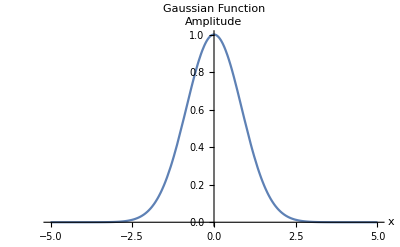

```mathematica
amplitude=1;
mean=0;
fwhm=2;

Plot[gaussian[x,amplitude,mean,fwhm],{x,-5,5},PlotRange->All,PlotLabel->"Gaussian Function",AxesLabel->{"x","Amplitude"}]
```

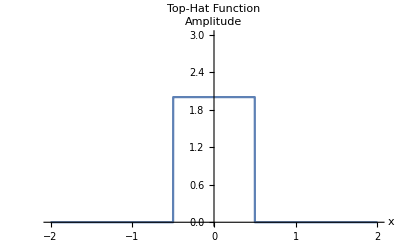

```mathematica
center=0;
width=1;
amplitude=2;

Plot[tophat[x,center,width,amplitude],{x,-2,2},PlotRange->{0,3},PlotLabel->"Top-Hat Function",AxesLabel->{"x","Amplitude"}]
```

```mathematica
ClearAll[w,d,a,c,x,y]
```

```mathematica
conv = FullSimplify[Convolve[gaussian[x,1,0,w],tophat[x,c,d,a],x,y], Assumptions->{w>0,a>0,d>0,c>0}]/.y->x
```

1/4 a w (Erf[((2 c+d-2 x) √Log[2])/w]+Erf[((-2 c+d+2 x) √Log[2])/w]) √(π/Log[2])

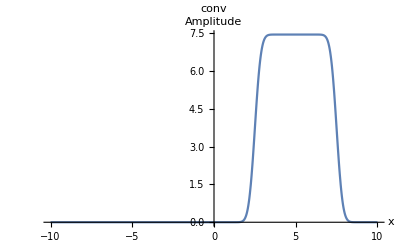

```mathematica
Plot[conv/.{w ->0.7, c->5,d->5, a -> 10},{x,-10,10},PlotRange->All,PlotLabel->"conv",AxesLabel->{"x","Amplitude"}]
```